max(-s/2,x-2 r)-min((3 s)/2,2 r+x)+2 s

Piecewise[{{2 s-4 r, 4 r<s+2 x∧4 r+2 x<3 s}, {-2 r+(3 s)/2-x, 4 r≥s+2 x∧4 r+2 x<3 s}, {-2 r+s/2+x, 4 r<s+2 x∧4 r+2 x≥3 s}}]

max(-s/2,x-2 r)-min((3 s)/2,2 r+x)+4 r

Piecewise[{{4 r-2 s, 4 r≥s+2 x∧4 r+2 x≥3 s}, {2 r-s/2-x, 4 r≥s+2 x∧4 r+2 x<3 s}, {2 r-(3 s)/2+x, 4 r<s+2 x∧4 r+2 x≥3 s}}]

Piecewise[{{2 s-4 r, 2 r<s∧4 r<s}, {(4 (s-2 r)^2)/s, 2 r<s∧4 r==s}, {(4 r-3 s)^2/(4 s), (4 r<3 s∧2 r≥s∧4 r≥s)∨(2 r<s∧4 r>s)}}]

Piecewise[{{4 r-2 s, 4 r≥3 s∧2 r≥s}, {-(12 r^2)/s+14 r-(15 s)/4, 4 r<3 s∧2 r==s}, {(s-4 r)^2/(4 s), 4 r<3 s∧((4 r>s∧2 r<s)∨2 r>s)}}]

-Graphics3D-

-Graphics3D-

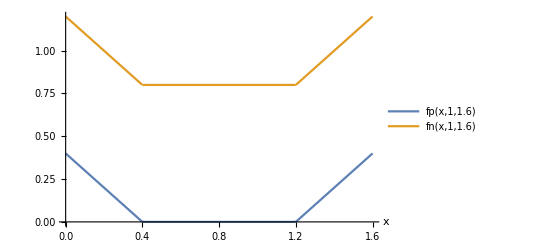

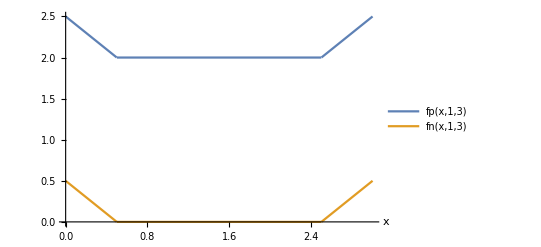

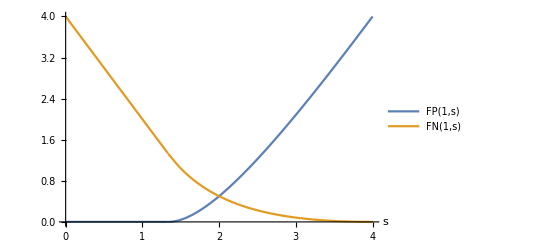

```mathematica
(*Assumptions*)
$Assumptions=Element[{r,s,x},Reals]&&r>0&&s>0&&x≥0&&x≤s;

(*Definitions*)
fp[x_,r_,s_]:=2s-(Min[x+2r,(3/2)s]-Max[x-2r,-s/2]);
fn[x_,r_,s_]:=4r-(Min[x+2r,(3/2)s]-Max[x-2r,-s/2]);
p[x_]:=1/s;
FP[r_,s_]=Integrate[fp[x,r,s]p[x],{x,0,s}];
FN[r_,s_]=Integrate[fn[x,r,s]p[x],{x,0,s}];

(*Prints*)
fp[x,r,s]//TraditionalForm
PiecewiseExpand[fp[x,r,s]] //Simplify//TraditionalForm
fn[x,r,s]//TraditionalForm
PiecewiseExpand[fn[x,r,s]] //Simplify // TraditionalForm
FP[r,s]//Simplify//TraditionalForm
FN[r,s]//Simplify//TraditionalForm

(*Plots*)
Plot3D[fp[x,1,s],{s,0,5},{x,0,s},AxesLabel->Automatic]
Plot3D[fn[x,1,s],{s,0,5},{x,0,s},AxesLabel->Automatic]
Plot3D[{fp[x,1,s],fn[x,1,s]},{s,0,5},{x,0,s},AxesLabel->Automatic,PlotLegends->"Expressions"]

Plot[{fp[x,1,1.6],fn[x,1,1.6]},{x,0,1.6},AxesLabel->Automatic,PlotLegends->"Expressions"]
Plot[{fp[x,1,3],fn[x,1,3]},{x,0,3},AxesLabel->Automatic,PlotLegends->"Expressions"]

Plot[{FP[1,s],FN[1,s]},{s,0,4},AxesLabel->Automatic,PlotLegends->"Expressions"]
```